### Start choosing the example:

```mathematica
t=14;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesData.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3},Adjacency Matrix→{{0,1,0},{0,0,1},{1,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1}},Switching Costs→{{1,2,3,S1},{3,2,1,S2}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->10,U1->95,S1->0, S2->0}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.336746 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
3 j13==10&&j15==0&&j18==0&&3 u37==305&&3 u38==295&&u39==95&&3 u41==305
and the rules are:
<|j17→10,u45→95,j14→j13,j16→10,j19→j18,j20→10-j13+j15+j18,j21→0,j22→0,jt23→j18,jt24→0,jt25→j15,jt26→0,jt27→j13-j15,jt28→10-j13+j15,jt29→j13,jt30→j18,jt31→j15,jt32→j13-j15,jt33→j18,jt34→10-j13+j15,jt35→0,jt36→0,u40→95,u42→-j13+j18+u37,u43→-j13+j18+u38,u44→10-j13+j18+u39,u46→u41|>

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.278448,Null}

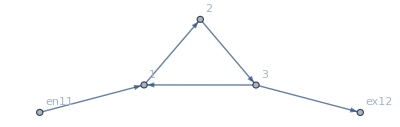

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j13→10/3,j14→10/3,j15→0,j16→10,j17→10,j18→0,j19→0,j20→20/3,j21→0,j22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→10/3,jt28→20/3,jt29→10/3,jt30→0,jt31→0,jt32→10/3,jt33→0,jt34→20/3,jt35→0,jt36→0,u37→305/3,u38→295/3,u39→95,u40→95,u41→305/3,u42→295/3,u43→95,u44→305/3,u45→95,u46→305/3|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0837197

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0710907

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0594929

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0491127

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0400205

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0322101

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0256235

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0201661

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0157188

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0121497

<|j13→1.58963,j14→1.58963,j15→0,j16→10,j17→10,j18→0,j19→0,j20→8.41037,j21→0,j22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→1.58963,jt28→8.41037,jt29→1.58963,jt30→0,jt31→0,jt32→1.58963,jt33→0,jt34→8.41037,jt35→0,jt36→0,u37→96.7804,u38→95.8902,u39→95.,u40→95,u41→96.7804,u42→95.8902,u43→95.,u44→96.7804,u45→95,u46→96.7804|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0860853

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0710361

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0577697

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0463679

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0367711

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0288412

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0223979

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0172426

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0131747

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0100035

<|j13→1.69447,j14→1.69447,j15→0,j16→10,j17→10,j18→0,j19→0,j20→8.30553,j21→0,j22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→1.69447,jt28→8.30553,jt29→1.69447,jt30→0,jt31→0,jt32→1.69447,jt33→0,jt34→8.30553,jt35→0,jt36→0,u37→96.948,u38→95.974,u39→95.,u40→95,u41→96.948,u42→95.974,u43→95.,u44→96.948,u45→95,u46→96.948|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0897687

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0684399

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0514944

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0383311

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0282808

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0207142

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0150832

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0109321

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00789502

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0056862

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00408702

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00293318

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00210277

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00150625

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00107832

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000771645

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000552022

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000394822

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000282344

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000201887

<|j13→1.89996,j14→1.89996,j15→0,j16→10,j17→10,j18→0,j19→0,j20→8.10004,j21→0,j22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→1.89996,jt28→8.10004,jt29→1.89996,jt30→0,jt31→0,jt32→1.89996,jt33→0,jt34→8.10004,jt35→0,jt36→0,u37→97.3694,u38→96.1847,u39→95.,u40→95,u41→97.3694,u42→96.1847,u43→95.,u44→97.3694,u45→95,u46→97.3694|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0442957

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0106646

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.00256779

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000618266

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.000148865

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.0000358433

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 8.63028×10^-6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.07798×10^-6

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 5.00332×10^-7

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.20469×10^-7

<|j13→3.13443,j14→3.13443,j15→0,j16→10,j17→10,j18→0,j19→0,j20→6.86557,j21→0,j22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→3.13443,jt28→6.86557,jt29→3.13443,jt30→0,jt31→0,jt32→3.13443,jt33→0,jt34→6.86557,jt35→0,jt36→0,u37→100.51,u38→97.7552,u39→95.,u40→95,u41→100.51,u42→97.7552,u43→95.,u44→100.51,u45→95,u46→100.51|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[8.70234×10^-15,ComplexInfinity]

<|j13→10/3,j14→10/3,j15→0,j16→10,j17→10,j18→0,j19→0,j20→20/3,j21→0,j22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→10/3,jt28→20/3,jt29→10/3,jt30→0,jt31→0,jt32→10/3,jt33→0,jt34→20/3,jt35→0,jt36→0,u37→305/3,u38→295/3,u39→95,u40→95,u41→305/3,u42→295/3,u43→95,u44→305/3,u45→95,u46→305/3|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],1,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.245827

<|j13→4.06478,j14→4.06478,j15→0,j16→10,j17→10,j18→0,j19→0,j20→5.93522,j21→0,j22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→4.06478,jt28→5.93522,jt29→4.06478,jt30→0,jt31→0,jt32→4.06478,jt33→0,jt34→5.93522,jt35→0,jt36→0,u37→105.681,u38→100.341,u39→95.,u40→95,u41→105.681,u42→100.341,u43→95.,u44→105.681,u45→95,u46→105.681|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.971962

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.00291

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

<|j13→0,j14→0,j15→0,j16→10,j17→10,j18→1.1545×10^151,j19→1.1545×10^151,j20→1.1545×10^151,j21→0,j22→0,jt23→1.1545×10^151,jt24→0,jt25→0,jt26→0,jt27→0,jt28→10,jt29→0,jt30→1.1545×10^151,jt31→0,jt32→0,jt33→1.1545×10^151,jt34→10,jt35→0,jt36→0,u37→0.,u38→0.,u39→95.,u40→95,u41→0.,u42→0.,u43→95.,u44→0.,u45→95,u46→0.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],4,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«1 more identical outputs»

<|j13→0,j14→0,j15→0,j16→10,j17→10,j18→6.12656×10^239,j19→6.12656×10^239,j20→6.12656×10^239,j21→0,j22→0,jt23→6.12656×10^239,jt24→0,jt25→0,jt26→0,jt27→0,jt28→10,jt29→0,jt30→6.12656×10^239,jt31→0,jt32→0,jt33→6.12656×10^239,jt34→10,jt35→0,jt36→0,u37→0.,u38→0.,u39→95.,u40→95,u41→0.,u42→0.,u43→95.,u44→0.,u45→95,u46→0.|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«1 more identical outputs»

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[√(Abs[3.25505603204617×10^333-1. j13+1. j18-IntM[-10+j13-j18]]^2+2 Abs[3.25505603204617×10^333-1. j13+1. j18-IntM[j13-j18]]^2),(√(Abs[3.25505603204617×10^333-1. j13+1. j18-IntM[-10+j13-j18]]^2+2 Abs[3.25505603204617×10^333-1. j13+1. j18-IntM[j13-j18]]^2))/(√3 Abs[3.25505603204617×10^333+0. j13+0. j18]),(√(Abs[3.25505603204617×10^333-1. j13+1. j18-IntM[-10+j13-j18]]^2+2 Abs[3.25505603204617×10^333-1. j13+1. j18-IntM[j13-j18]]^2))/(√(Abs[-10+j13-j18+IntM[-10+j13-j18]]^2+2 Abs[j13-j18+IntM[j13-j18]]^2))]

ReplaceAll::reps: {u38==u42&&u39==95&&u41==u44&&u43==95&&j13-j18-u37+u42==j13-j18+IntM[j13-j18]&&j13-j18-u38+u43==j13-j18+IntM[j13-j18]&&-10+j13-j18-u39+u44==-10+j13-j18+IntM[-10+j13-j18]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

AssociateTo::invlb: The argument u38==u42&&u39==95&&u41==u44&&u43==95&&j13-j18-u37+u42==j13-j18+IntM[j13-j18]&&j13-j18-u38+u43==j13-j18+IntM[j13-j18]&&-10+j13-j18-u39+u44==-10+j13-j18+IntM[-10+j13-j18] is not a list, Rule, or Association.

ReplaceAll::reps: {u38==u42&&u39==95&&u41==u44&&u43==95&&j13-j18-u37+u42==j13-j18+IntM[j13-j18]&&j13-j18-u38+u43==j13-j18+IntM[j13-j18]&&-10+j13-j18-u39+u44==-10+j13-j18+IntM[-10+j13-j18]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],8,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«5 more identical outputs»

<|j13→3.33327,j14→3.33327,j15→0,j16→10,j17→10,j18→0,j19→0,j20→6.66673,j21→0,j22→0,jt23→0,jt24→0,jt25→0,jt26→0,jt27→3.33327,jt28→6.66673,jt29→3.33327,jt30→0,jt31→0,jt32→3.33327,jt33→0,jt34→6.66673,jt35→0,jt36→0,u37→101.667,u38→98.3333,u39→95.,u40→95,u41→101.667,u42→98.3333,u43→95.,u44→101.667,u45→95,u46→101.667|>